```mathematica
(* WALKING KINEMATICS: STICK FIGURE PLUS 3D JOINT ANGLES - Filtered, Archive data*)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(*This code requires input of single trial at a time*)
(*TrialMatrix information
KM01_RUN_02 [1,1]
KM02_RUN_01[2,1], KM02_RUN_02[2,2], KM02_RUN_09[2,3]
KM04_RUN_09[3,1], KM04_RUN_11[3,2], KM04_RUN_12[3,3]
KM05_RUN_04[4,1], KM05_RUN_08[4,2]
KM06_RUN_11[5,1], KM06_RUN_12[5,2], KM06_RUN_13[5,3], KM06_RUN_15[5,4], KM06_RUN_16[5,5]
KM07_RUN_14[6,1], KM07_RUN_16[6,2], KM07_RUN_17[6,3]
KM08_RUN_09[7,1], KM08_RUN_10[7,2]
KM23_RUN_01[8,1], KM23_RUN_02[8,2], KM23_RUN_03[8,3], KM23_RUN_05[8,4]*)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(* Determine operating system *)

os=$OperatingSystem;
frogworkpath="C:\\YOUR FILE DIRECTORY HERE\\" (*Set your main file directory, not to the folder where raw or archived data are stored*)
(*e.g. frogworkpath="C:\\Users\\Documents\\"*)
(*for Mac users change "C:\\" to "\\Volumes\\"*)

dataDirectory="YOUR DIRECTORY TO ARCHIVED .DAT DATA"; (*Set the directory where archived data from the "Code to Archive Data" notebook was exported to*)


setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];
Print["Directory set"]
(***********************************************************************************)

(* Determine animal filename *)

Needs["GraphUtilities`"]
whatFrog[filename_]:=StringTake[filename,{3,4}](*extracts the animal number*)
trialFiles=FileNames[];
ntrials=Length[trialFiles];
trialMatrix=GatherBy[trialFiles,whatFrog];(*organize the trials in a matrix *)
ExpressionTreePlot[trialMatrix,VertexLabeling->Tooltip];
Print["animal name set"]
(******************************************************************************************)

(*INPUT - Type Animal Filename *)

animalfilename=trialMatrix[[8,4]] (*Change this to match trial matrix information above*)
(*e.g. animalfilename=trailMatrix[[8,4]] uses KM23_RUN_05*)

(******************************************************************************************)

(* Import raw data *)

allrawtrialdata=Import[animalfilename,"Data"];
Print["raw trial data imported"]
(***********************************************************************************)

(* Import metadata*)
(*Set the directory where the METADATA.xlsx is saved*)

(*SET DIRECTORY*)
dataDirectory="YOUR DIRECTORY TO METADATA.xlsx FILE";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

importedmetadata=Import["METADATA.xlsx","Data"];
metadata=importedmetadata[[1,2;;24,All]];
Print["Directory set"]
(***********************************************************************************)

(* Metadata file map: Locate information *)

filenamerow=Flatten[Position[metadata,animalfilename]][[1]];

SVL=metadata[[filenamerow,2]];
Framerate=metadata[[filenamerow,3]];
TotalNumberRawFramesDigitised=metadata[[filenamerow,4]];
FirstFrame=metadata[[filenamerow,6]];
FinalFrame=metadata[[filenamerow,7]];
EndofFrames=metadata[[filenamerow,8]]; (*Total number of frames from first to final*)
StartofStance=metadata[[filenamerow,9]];
StartofSwing=metadata[[filenamerow,10]];
StartofLimbCycle=metadata[[filenamerow,11]];
EndofLimbCycle=metadata[[filenamerow,12]];
SingleStrideFrameCount=metadata[[filenamerow,13]];
SingleStrideTimeDuration=metadata[[filenamerow,14]];
AnimalDataTrialforexporting=metadata[[filenamerow,16]];
Print["METADATA imported"]
(***********************************************************************************)

(* Load filtering package/info *)

Needs["Biomechanics`"]; (*"Biomechanics" notebook provided*)

Duration=EndofFrames/Framerate;
DT=1/Framerate;(*sample interval, s*)
FC=30 ;(*cutoff frequency*)
Print["got biomechanics package"]
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(* Partition raw data for filtering*)

nonfilteredend=Dimensions[allrawtrialdata][[1]];
allrawLMdata=Table[
fullframe=allrawtrialdata[[i]];
Partition[fullframe,3]
,{i,1,nonfilteredend}];

allrawLMdataX=Table[allrawLMdata[[All,i,1]],{i,1,12}];
allrawLMdataY=Table[allrawLMdata[[All,i,2]],{i,1,12}];
allrawLMdataZ=Table[allrawLMdata[[All,i,3]],{i,1,12}];

(*****************************************************************************************)

(* Apply filter to raw XYZ data *)

allLMdataX=Table[BFilterR[allrawLMdataX[[i,All]],FC,DT],{i,1,12}];
allLMdataY=Table[BFilterR[allrawLMdataY[[i,All]],FC,DT],{i,1,12}];
allLMdataZ=Table[BFilterR[allrawLMdataZ[[i,All]],FC,DT],{i,1,12}];

Print["Data filtered"]
```

Data filtered

```mathematica
(*****************************************************************************************)

(* Re-join filtered data *)

end=Length[allLMdataX[[1]]]
allLMdata =Transpose[Table[Join[{allLMdataX[[i,f]]},{allLMdataY[[i,f]]},{allLMdataZ[[i,f]]}],{i,1,12},{f,1,end}]];

Dimensions[allLMdata]

(******************************************************************************************)

(* Partition per marker to build stick figure *)

LM1allframes=allLMdata[[All,1,All]];
LM2allframes=allLMdata[[All,2,All]];
LM3allframes=allLMdata[[All,3,All]];
LM4allframes=allLMdata[[All,4,All]];
LM5allframes=allLMdata[[All,5,All]];
LM6allframes=allLMdata[[All,6,All]];
LM7allframes=allLMdata[[All,7,All]];
LM8allframes=allLMdata[[All,8,All]];
LM9allframes=allLMdata[[All,9,All]];
LM10allframes=allLMdata[[All,10,All]];
LM11allframes=allLMdata[[All,11,All]];
LM12allframes=allLMdata[[All,12,All]];
```

167

{167,12,3}

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(* Build stick figure *)

(* Build each element of stick figure *)
(* 1. Body triangles *)

BodyTriangle1LMJoin=Table[Join[LM5allframes[[f]],LM6allframes[[f]],LM7allframes[[f]],LM5allframes[[f]]],{f,1,end}];
BodyTriangle1=Table[singleframe=BodyTriangle1LMJoin[[f]];Partition[singleframe,3],{f,1,end}];


BodyTriangle2LMJoin=Table[Join[LM8allframes[[f]],LM9allframes[[f]],LM10allframes[[f]],LM8allframes[[f]]],{f,1,end}];
BodyTriangle2=Table[singleframe=BodyTriangle2LMJoin[[f]];Partition[singleframe,3],{f,1,end}];

(* 2. Leg *)

LegLMJoin=Table[Join[LM1allframes[[f]],LM2allframes[[f]],LM3allframes[[f]],LM4allframes[[f]]],{f,1,end}];
Leg=Table[singleframe=LegLMJoin[[f]];Partition[singleframe,3],{f,1,end}];

(* 3. Midline *)

MidlineLMJoin=Table[Join[LM10allframes[[f]],LM11allframes[[f]],LM12allframes[[f]],LM5allframes[[f]]],{f,1,end}];
Midline=Table[singleframe=MidlineLMJoin[[f]];Partition[singleframe,3],{f,1,end}];

(***************************************************************************)

(* Plot the figure *)

Manipulate[
singleframeBT1=BodyTriangle1[[frame]];
BT1graph1=Graphics3D[Line[singleframeBT1]];
BT1graph2=ListPointPlot3D[singleframeBT1,PlotStyle->Red];
BT1plot=Show[BT1graph1,BT1graph2];

singleframeBT2=BodyTriangle2[[frame]];
BT2graph1=Graphics3D[Line[singleframeBT2]];
BT2graph2=ListPointPlot3D[singleframeBT2,PlotStyle->Red];
BT2plot=Show[BT2graph1,BT2graph2];

singleframeLeg=Leg[[frame]];
Lgraph1=Graphics3D[Line[singleframeLeg]];
Lgraph2=ListPointPlot3D[singleframeLeg,PlotStyle->Red];
Legplot=Show[Lgraph1,Lgraph2];

singleframeMidLine=Midline[[frame]];
MidLinegraph1=Graphics3D[Line[singleframeMidLine]];
MidLinegraph2=ListPointPlot3D[singleframeMidLine,PlotStyle->Red];
MidLineplot=Show[MidLinegraph1,MidLinegraph2];

FrogStickFigure=Show[BT1plot,BT2plot,Legplot,MidLineplot,PlotRange->{{-50,200},{-50,200},{-50,100}},AspectRatio->1]

,{frame,1,end,1}]; (*remove this semicolon to view 3D stick figure*)
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(* Mathematically tether the frog *)

(*1. Chunk out required frames - the good frames of calibrated steady forward locomotion(first frame-final frame) - from this point onwards to analyse all data it'll be 1 to end of frames*)

chunkedLMdata=allLMdata[[IntegerPart[FirstFrame];;IntegerPart[FinalFrame]]];
Dimensions[chunkedLMdata]


(*2. tether the frog at the hip LM *)

HipTetheredLMs=Table[
CurrentLMs=chunkedLMdata[[frame]];
Origin={0,0,0};
HipDifference=CurrentLMs[[4]]-Origin;
TetheredLMs=Table[CurrentLMs[[i]]-HipDifference,{i,1,12}]
,{frame,1,EndofFrames}];

(* 3. create new tethered LMs *)
(* {frames,xyz} *)

LM1allframesTH=HipTetheredLMs[[All,1,All]];
LM2allframesTH=HipTetheredLMs[[All,2,All]];
LM3allframesTH=HipTetheredLMs[[All,3,All]];
LM4allframesTH=HipTetheredLMs[[All,4,All]];
LM5allframesTH=HipTetheredLMs[[All,5,All]];
LM6allframesTH=HipTetheredLMs[[All,6,All]];
LM7allframesTH=HipTetheredLMs[[All,7,All]];
LM8allframesTH=HipTetheredLMs[[All,8,All]];
LM9allframesTH=HipTetheredLMs[[All,9,All]];
LM10allframesTH=HipTetheredLMs[[All,10,All]];
LM11allframesTH=HipTetheredLMs[[All,11,All]];
LM12allframesTH=HipTetheredLMs[[All,12,All]];
```

{166,12,3}

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(* Build tethered stick figure *)

(* Build each element of tethered stick figure *)

(* 1. Body triangles *)

BodyTriangle1LMJoinTH=Table[Join[LM5allframesTH[[f]],LM6allframesTH[[f]],LM7allframesTH[[f]],LM5allframesTH[[f]]],{f,1,EndofFrames}];
BodyTriangle1TH=Table[singleframe=BodyTriangle1LMJoinTH[[f]];Partition[singleframe,3],{f,1,EndofFrames}];


BodyTriangle2LMJoinTH=Table[Join[LM8allframesTH[[f]],LM9allframesTH[[f]],LM10allframesTH[[f]],LM8allframesTH[[f]]],{f,1,EndofFrames}];
BodyTriangle2TH=Table[singleframe=BodyTriangle2LMJoinTH[[f]];Partition[singleframe,3],{f,1,EndofFrames}];

(* 2. Leg *)

LegLMJoinTH=Table[Join[LM1allframesTH[[f]],LM2allframesTH[[f]],LM3allframesTH[[f]],LM4allframesTH[[f]]],{f,1,EndofFrames}];
LegTH=Table[singleframe=LegLMJoinTH[[f]];Partition[singleframe,3],{f,1,EndofFrames}];

(* 3. Midline *)

MidlineLMJoinTH=Table[Join[LM10allframesTH[[f]],LM11allframesTH[[f]],LM12allframesTH[[f]],LM5allframesTH[[f]]],{f,1,EndofFrames}];
MidlineTH=Table[singleframe=MidlineLMJoinTH[[f]];Partition[singleframe,3],{f,1,EndofFrames}];

(* 4. Hiplines *)

HipLinesraw=Table[
LM4singleframeTH=LM4allframesTH[[i]];
LM7singleframeTH=LM7allframesTH[[i]];
HipLinexy=LM4singleframeTH+LM7singleframeTH;
HipLinesJoined=Join[HipLinexy,LM4singleframeTH]
,{i,1,EndofFrames}];

HipLines=Table[
HipLinessingleframe=HipLinesraw[[i]];
Partition[HipLinessingleframe,3]
,{i,1,EndofFrames}];

(***************************************************************************)

(* Plot the figure *)

Manipulate[
singleframeBT1TH=BodyTriangle1TH[[frame]];
BT1graph1TH=Graphics3D[Line[singleframeBT1TH]];
BT1graph2TH=ListPointPlot3D[singleframeBT1TH,PlotStyle->Red];
BT1plotTH=Show[BT1graph1TH,BT1graph2TH];

singleframeBT2TH=BodyTriangle2TH[[frame]];
BT2graph1TH=Graphics3D[Line[singleframeBT2TH]];
BT2graph2TH=ListPointPlot3D[singleframeBT2TH,PlotStyle->Red];
BT2plotTH=Show[BT2graph1TH,BT2graph2TH];

singleframeLegTH=LegTH[[frame]];
Lgraph1TH=Graphics3D[Line[singleframeLegTH]];
Lgraph2TH=ListPointPlot3D[singleframeLegTH,PlotStyle->Red];
LegplotTH=Show[Lgraph1TH,Lgraph2TH];

singleframeMidLineTH=MidlineTH[[frame]];
MidLinegraph1TH=Graphics3D[Line[singleframeMidLineTH]];
MidLinegraph2TH=ListPointPlot3D[singleframeMidLineTH,PlotStyle->Red];
MidLineplotTH=Show[MidLinegraph1TH,MidLinegraph2TH];

singleframeHiplinesplot=HipLines[[frame]];
Hiplinesplot1=Graphics3D[Line[singleframeHiplinesplot]];
Hiplinesplot2=ListPointPlot3D[singleframeHiplinesplot,PlotStyle->Green];
Hiplineforstickfigure=Show[Hiplinesplot1,Hiplinesplot2];


FrogStickFigureTH=Show[BT1plotTH,BT2plotTH,LegplotTH,MidLineplotTH,Hiplineforstickfigure,PlotRange->{{-50,200},{-50,200},{-50,100}},AspectRatio->1]

,{frame,1,EndofFrames,1}]; (*remove this semicolon to view 3D stick figure tethered at the hip*)
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(* Find 3D joint angles *)

(* Define LM data required - assuming straight line for body *)

HipLMdataTH=LM4allframesTH;
KneeLMdataTH=LM3allframesTH;
HipLineXYLMdataTH=HipLines[[All,1,All]];
AnkleLMdataTH=LM2allframesTH;
TmtLMdataTH=LM1allframesTH;

(******************************************************************************************)

(* Find vector angles *)

(*Hip angle*)
Kneecorrectedforhip=KneeLMdataTH-HipLMdataTH;
Kneecorrectedforhipxy=Kneecorrectedforhip[[All,{1,2}]];

HipLineXYcorrectedforhip=HipLineXYLMdataTH-HipLMdataTH;
HipLineXYcorrectedforhipxy=HipLineXYcorrectedforhip[[All,{1,2}]];

(*HipLineYZcorrectedforhip=HipLineYZLMdataTH-HipLMdataTH;*)

(*Knee angle*)
Hipcorrectedforknee=HipLMdataTH-KneeLMdataTH;
Anklecorrectedforknee=AnkleLMdataTH-KneeLMdataTH;

(*Ankle angle*)
Kneecorrectedforankle=KneeLMdataTH-AnkleLMdataTH;
Tmtcorrectedforankle=TmtLMdataTH-AnkleLMdataTH;

(*Vector angles*)

HipAnglexy=Table[VectorAngle[Kneecorrectedforhipxy[[f]],HipLineXYcorrectedforhipxy[[f]]],{f,1,EndofFrames}];


HipAngle=Table[VectorAngle[Kneecorrectedforhip[[f]],HipLineXYcorrectedforhip[[f]]],{f,1,EndofFrames}];
KneeAngle=Table[VectorAngle[Hipcorrectedforknee[[f]],Anklecorrectedforknee[[f]]],{f,1,EndofFrames}];
AnkleAngle=Table[VectorAngle[Kneecorrectedforankle[[f]],Tmtcorrectedforankle[[f]]],{f,1,EndofFrames}];

(******************************************************************************************)

(* Arrange 3D vector angle data into correct units *)

Degrees=360./(2Pi);
xValues=Table[x/Framerate,{x,1,EndofFrames}];

HipAngleData=Thread[{xValues,(HipAngle*Degrees)}];
HipXYAngleData=Thread[{xValues,(HipAnglexy*Degrees)}];
KneeAngleData=Thread[{xValues,(KneeAngle*Degrees)}];
AnkleAngleData=Thread[{xValues,(AnkleAngle*Degrees)}];
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

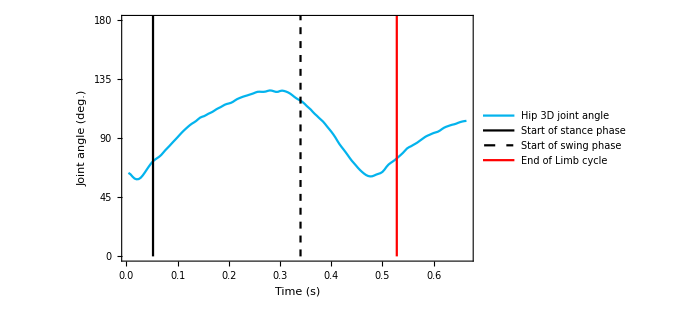

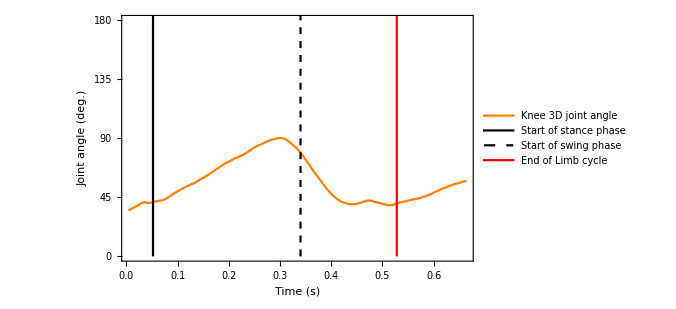

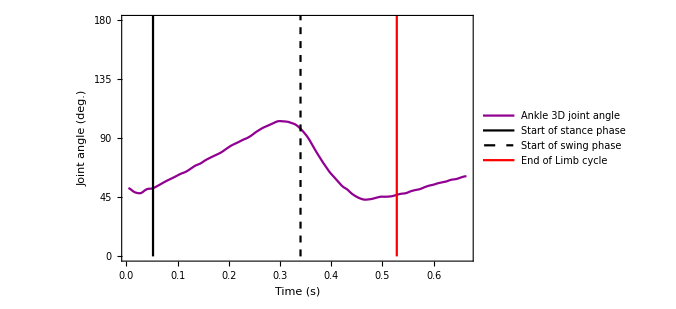

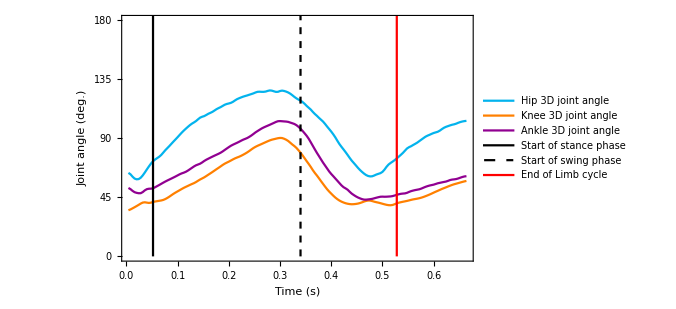

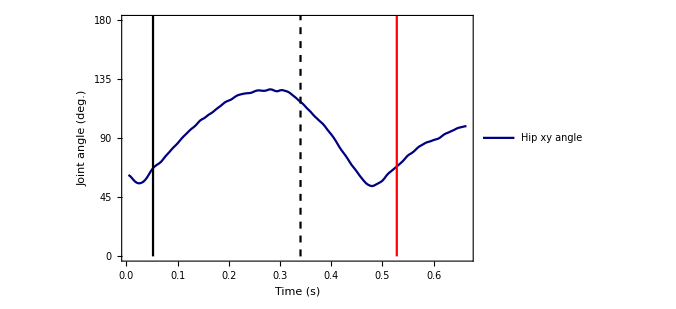

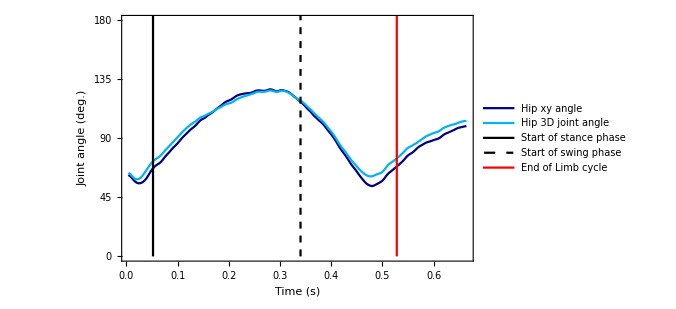

```mathematica
(* Plot 3D joint angles *)

(* Define plot setting and style *)

HipLineStyle={Setting[0.011764705882352941],Thick};
KneeLineStyle={Setting[1.],Thick};
AnkleLineStyle={Setting[0.5686274509803921],Thick};
HipXYLineStyle={Setting[0.],Thick};
HipYZLineStyle={Setting[0.2627450980392157],Thick};

JointAngleAxesStyle={PlotRange->{{(1/Framerate),(EndofFrames/Framerate)},{0,180}},Frame->{{True,False},{True,False}},FrameLabel->{"Time (s)","Joint angle (deg.)"},LabelStyle->{{FontSize->12},(FontFamily->"Calibri")},FrameTicks->{Automatic,{0,{45/2,""},45,{(45/2)+45,""},90,{(45/2)+90,""},135,{(45/2)+135,""},180}}};

JointAngleGraphStyle={Background->None,ImageSize->500};

StancePhaseStyle=PlotStyle->{Black,Thick};
SwingPhaseStyle=PlotStyle->{Black,Thick,Dashed};
EndofLimbCycleStyle=PlotStyle->{Red,Thick};

StartStanceRange={{(N[StartofStance/Framerate]),0},{(N[StartofStance/Framerate]),200}};
EndofLimbCycleRange={{(N[EndofLimbCycle/Framerate]),0},{(N[EndofLimbCycle/Framerate]),200}};
StartSwingRange={{(N[StartofSwing/Framerate]),0},{(N[StartofSwing/Framerate]),200}};

JointAngleLegend=LineLegend[{Setting[0.011764705882352941],Setting[1.],Setting[0.5686274509803921],{Black,Thick},{Black,Thick,Dashed},{Red,Thick}},{"Hip 3D joint angle","Knee 3D joint angle","Ankle 3D joint angle","Start of stance phase","Start of swing phase","End of Limb cycle"},LabelStyle->{Large,(FontFamily->"Calibri")}];
HipJointAngleLegend=LineLegend[{Setting[0.011764705882352941],{Black,Thick},{Black,Thick,Dashed},{Red,Thick}},{"Hip 3D joint angle","Start of stance phase","Start of swing phase","End of Limb cycle"},LabelStyle->{Large,(FontFamily->"Calibri")}];
KneeJointAngleLegend=LineLegend[{Setting[1.],{Black,Thick},{Black,Thick,Dashed},{Red,Thick}},{"Knee 3D joint angle","Start of stance phase","Start of swing phase","End of Limb cycle"},LabelStyle->{Large,(FontFamily->"Calibri")}];
AnkleJointAngleLegend=LineLegend[{Setting[0.5686274509803921],{Black,Thick},{Black,Thick,Dashed},{Red,Thick}},{"Ankle 3D joint angle","Start of stance phase","Start of swing phase","End of Limb cycle"},LabelStyle->{Large,(FontFamily->"Calibri")}];

HipXYandYZLegend=LineLegend[{Setting[0.],Setting[0.2627450980392157]},{"Hip xy angle","Hip yz angle"},LabelStyle->{Large,(FontFamily->"Calibri")}];
HipXYLegend=LineLegend[{Setting[0.]},{"Hip xy angle"},LabelStyle->{Large,(FontFamily->"Calibri")}];
(*HipYZLegend=LineLegend[{Setting[0.2627450980392157],},{"Hip yz angle"},LabelStyle->{Large,(FontFamily->"Calibri")}];*)



HipXYand3DAngleLegend=LineLegend[{Setting[0.],Setting[0.011764705882352941],{Black,Thick},{Black,Thick,Dashed},{Red,Thick}},{"Hip xy angle","Hip 3D joint angle","Start of stance phase","Start of swing phase","End of Limb cycle"},LabelStyle->{Large,(FontFamily->"Calibri")}];

(****************************************************************************************************)

(* Plot the graphs *)

StartofStanceLine=ListLinePlot[StartStanceRange,StancePhaseStyle];
EndofCycleLine=ListLinePlot[EndofLimbCycleRange,EndofLimbCycleStyle];
StartofSwingLine=ListLinePlot[StartSwingRange,SwingPhaseStyle];

(* Hip plot *)
Hip3DAnglenophaselinesPlot=ListLinePlot[HipAngleData,JointAngleAxesStyle,JointAngleGraphStyle,PlotStyle->HipLineStyle,PlotLegends->HipJointAngleLegend];
Hip3DAnglePlot=Show[Hip3DAnglenophaselinesPlot,StartofStanceLine,EndofCycleLine,StartofSwingLine]

(* Knee plot *)
Knee3DAnglenophaselinesPlot=ListLinePlot[KneeAngleData,JointAngleAxesStyle,JointAngleGraphStyle,PlotStyle->KneeLineStyle,PlotLegends->KneeJointAngleLegend];
Knee3DAnglePlot=Show[Knee3DAnglenophaselinesPlot,StartofStanceLine,EndofCycleLine,StartofSwingLine]

(* Ankle plot *)
Ankle3DAnglenophaselinesPlot=ListLinePlot[AnkleAngleData,JointAngleAxesStyle,JointAngleGraphStyle,PlotStyle->AnkleLineStyle,PlotLegends->AnkleJointAngleLegend];
Ankle3DAnglePlot=Show[Ankle3DAnglenophaselinesPlot,StartofStanceLine,EndofCycleLine,StartofSwingLine]

(* 3D joint angle plot - all on same graph *)
Hip3DAnglenophaselinesalllegendPlot=ListLinePlot[HipAngleData,JointAngleAxesStyle,JointAngleGraphStyle,PlotStyle->HipLineStyle,PlotLegends->JointAngleLegend];
Knee3DAnglenophaselinesnolegendPlot=ListLinePlot[KneeAngleData,JointAngleAxesStyle,JointAngleGraphStyle,PlotStyle->KneeLineStyle];
Ankle3DAnglenophaselinesnolegendPlot=ListLinePlot[AnkleAngleData,JointAngleAxesStyle,JointAngleGraphStyle,PlotStyle->AnkleLineStyle];

All3DJointAnglePlot=Show[Hip3DAnglenophaselinesalllegendPlot,Knee3DAnglenophaselinesnolegendPlot,Ankle3DAnglenophaselinesnolegendPlot,StartofStanceLine,EndofCycleLine,StartofSwingLine]

(* Hip XY angle plot *)
HipXYAnglenophaselinesPlot=ListLinePlot[HipXYAngleData,JointAngleAxesStyle,JointAngleGraphStyle,PlotStyle->HipXYLineStyle,PlotLegends->HipXYLegend];
HipXYAnglePlot=Show[HipXYAnglenophaselinesPlot,StartofStanceLine,EndofCycleLine,StartofSwingLine]


(* Hip xy and yz joint angle plots - all on same graph *)
(*HipXYAnglenophaselinesxyyzlegendPlot=ListLinePlot[HipXYAngleData,JointAngleAxesStyle,JointAngleGraphStyle,PlotStyle->HipXYLineStyle,PlotLegends->HipXYandYZLegend];*)

HipXYandYZPlot=Show[HipXYAnglenophaselinesxyyzlegendPlot,StartofStanceLine,EndofCycleLine,StartofSwingLine]

(* Hip xy and 3D joint angle plots - all on same graph *)
HipXYAnglenophaselinesxy3dlegendPlot=ListLinePlot[HipXYAngleData,JointAngleAxesStyle,JointAngleGraphStyle,PlotStyle->HipXYLineStyle,PlotLegends->HipXYand3DAngleLegend];
Hip3DAnglenophaselinesnolegendPlot=ListLinePlot[HipAngleData,JointAngleAxesStyle,JointAngleGraphStyle,PlotStyle->HipLineStyle];

HipXYand3DPlot=Show[HipXYAnglenophaselinesxy3dlegendPlot,Hip3DAnglenophaselinesnolegendPlot,StartofStanceLine,EndofCycleLine,StartofSwingLine]
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(* Crop 3D joint angle data to one hindlimb cycle *)

HipAngleOneLimbCycle=HipAngleData[[IntegerPart[StartofLimbCycle];;IntegerPart[EndofLimbCycle],2]];
KneeAngleOneLimbCycle=KneeAngleData[[IntegerPart[StartofLimbCycle];;IntegerPart[EndofLimbCycle],2]];
AnkleAngleOneLimbCycle=AnkleAngleData[[IntegerPart[StartofLimbCycle];;IntegerPart[EndofLimbCycle],2]];
HipXYAngleOneLimbCycle=HipXYAngleData[[IntegerPart[StartofLimbCycle];;IntegerPart[EndofLimbCycle],2]];


FramesinOneLimbCycle=EndofLimbCycle-StartofLimbCycle+1;

xValuesOneLimbCycle=Table[x/Framerate,{x,1,IntegerPart[FramesinOneLimbCycle]}];

HipAngleDataOneLimbCyle=Thread[{xValuesOneLimbCycle,HipAngleOneLimbCycle}];
KneeAngleDataOneLimbCyle=Thread[{xValuesOneLimbCycle,KneeAngleOneLimbCycle}];
AnkleAngleDataOneLimbCyle=Thread[{xValuesOneLimbCycle,AnkleAngleOneLimbCycle}];
HipXYAngleDataOneLimbCyle=Thread[{xValuesOneLimbCycle,HipXYAngleOneLimbCycle}];
HipYZAngleDataOneLimbCyle=Thread[{xValuesOneLimbCycle,HipYZAngleOneLimbCycle}];

(******************************************************************************************)

(*Add in cycle event data*)

(*Get frame number of start of swing relative to start of stance*)

StartofSwingOneLimbCycle=StartofSwing-StartofLimbCycle;

(******************************************************************************************)

(* Export data *)

(*EXPORT 3D JOINT ANGLE DATA - ONE LIMB CYCLE*)

dataDirectory="YOUR DIRECTORY TO EXPORT 3D JOINT ANGLE DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

Export[StringJoin[AnimalDataTrialforexporting,"_","Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx"],HipAngleDataOneLimbCyle];
Export[StringJoin[AnimalDataTrialforexporting,"_","Knee 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx"],KneeAngleDataOneLimbCyle];
Export[StringJoin[AnimalDataTrialforexporting,"_","Ankle 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx"],AnkleAngleDataOneLimbCyle];


(*EXPORT HIP COMPONENT ANGLE DATA - ONE LIMB CYCLE*)

dataDirectory="YOUR DIRECTORY TO EXPORT HIP COMPONENT ANGLE DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

Export[StringJoin[AnimalDataTrialforexporting,"_","Hip XY Joint Angle Data - One Limb Cycle - FILTERED.xlsx"],HipXYAngleDataOneLimbCyle];
(*Export[StringJoin[AnimalDataTrialforexporting,"_","Hip YZ Joint Angle Data - One Limb Cycle - FILTERED.xlsx"],HipYZAngleDataOneLimbCyle];*)


(*Export relative start of swing frame number*)

dataDirectory="YOUR DIRECTORY TO EXPORT STRIDE CYCLE DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

Export[StringJoin[AnimalDataTrialforexporting,"_","Start of Swing relative frame number.xlsx"],StartofSwingOneLimbCycle];

Print["EXPORTED"]

(******************************************************************************************)
```

EXPORTED

```mathematica
(*end of code*)
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```